### a)

```mathematica
Clear["Global`*"]
r[r_]=μ*r-r^3;
θ[r_]=ω+ν*r^2;

s = Solve[r[r]==0,{r}]
```

```mathematica
{{r->0},{r->-√μ},{r->√μ}}
p = (Sqrt[μ]*θ[Sqrt[μ]])/(2*π*Sqrt[μ])
```

{{r→0},{r→-√μ},{r→√μ}}

(μ ν+ω)/(2 π)

### b)

```mathematica
X1dot[X1_,X2_]:=1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2dot[X1_,X2_]:=X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
F1:=X1'[t]==1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3;
F2:=X2'[t]==X1[t]+1/10X2[t]+X1[t]*X2[t]+X1[t]^3-X2[t]^3-X1[t]^2*X2[t];
LC =NDSolve[{F1,F2,X1[0]==X2[0]==0.01},{X1,X2},{t,0,100}];
traj = ParametricPlot[
Evaluate[{X1[t],X2[t]}/.{LC},{t,0,100},PlotStyle->{Red}]]/.
Line[x_]->{Arrowheads[{0,0.06,0.06,0}],Arrow[x]},{-0.5,0.5};

plot = StreamPlot[{X1dot[X1,X2], X2dot[X1,X2]},{X1,-1,1},{X2,-1,1},FrameLabel->{"X1","X2"}];
Show[plot,traj]
```

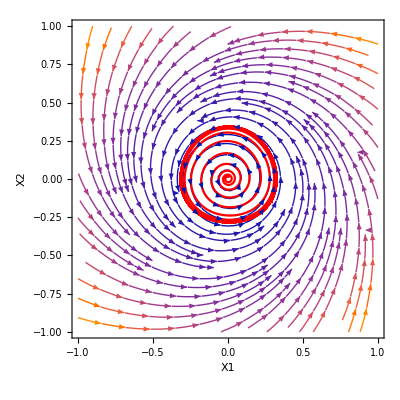

### c)

```mathematica
(*Comparing coefficients one can see that μ=1/10, ω=1, ν=1 makes the systems identifcal*)
```

### d)

```mathematica
Clear["Global`*"]
μ=1/10;ω=1;ν=1;T=2 πμ ν+ω;
```

### e)